# The basic example

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
f[z_]=FullSimplify[(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1)];
z0=.5+.5I;
iter=100000;
opac=.1;
AbsoluteTiming[Image[Graphics[{Black,Opacity[opac],PointSize[Tiny],Point@ReIm@NestList[f,z0,iter]}],ImageResolution->50,ImageSize->Large]]
```

{0.874858,-Graphics-}

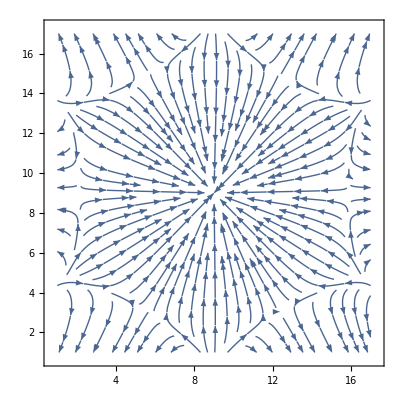

```mathematica
ListStreamPlot[Table[{Re[f[x+I y]],Im[f[x+ I y]]},{x,-.8,.8,.1},{y,-.8,.8,.1}]]
```

### Can we get 1,000,000 iterations plotted in under 4 seconds?

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
width=150;
height=150;
xmin=-.8;
xmax=.8;
xwidth=xmax-xmin;
ymin=-.8;
ymax=.8;
ywidth=ymax-ymin;
f[z_]=FullSimplify[(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1)];
pre[z_]=FullSimplify[Quotient[{width,height}*({Re[z],Im[z]}-{xmin,ymin}),{xwidth,ywidth}]];
z0=.5+.5I;
iter=100000;
data=ConstantArray[0.0,{width,height}];(* faster than SparseArray*)
```

```mathematica
AbsoluteTiming[Do[
{arrayx,arrayy}=pre[z0];
z0=f[z0];,{k,1,iter}]]
```

{0.814194,Null}

```mathematica
AbsoluteTiming[Do[

z0=f[z0];,{k,1,iter}]]
```

{40.2877,Null}

```mathematica
data=ConstantArray[0,{width,height}];
AbsoluteTiming[Do[
data[[RandomInteger[{1,width}],RandomInteger[{1,height}]]]++;
,{k,1,iter}]]
ArrayPlot[data]
```

{0.343583,Null}

-Graphics-

```mathematica
AbsoluteTiming[Do[
RandomInteger[{1,width}];
RandomInteger[{1,height}];
,{k,1,iter}]]
```

{0.132364,Null}

```mathematica
q[iterations_] = Module[{},
current = z0;
AbsoluteTiming[Do[
{arrayx,arrayy}=pre[current];
data[[arrayx,arrayy]]++;
current =f[current];,{k,1,iterations}]];
(*ArrayPlot[Log[data]+.01]];*)
q[100000]
```

```mathematica
data = ConstantArray[0,{width,height}];
subIter = 100;
current = z0;
AbsoluteTiming[Do[
l=ReIm@NestList[f,current,iter/subIter];
current =
```

```mathematica
l = NestList[f,z0,5]
```

{0.5+0.5 ⅈ,-0.225+0.025 ⅈ,0.549302-0.0614022 ⅈ,-0.581803+0.0971848 ⅈ,0.490309-0.142551 ⅈ,-0.68091+0.233823 ⅈ}

```mathematica
{0.8563038,Null}
```

{0.856304,Null}

```mathematica
{0.9137822,Null}
```

{0.913782,Null}

```mathematica
AbsoluteTiming[ArrayPlot[Log[data+.01]]]
AbsoluteTiming[Graphics[Raster[1/(data+1)]]]
```

{0.041849,-Graphics-}

{0.000849,-Graphics-}

# An animated example

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
(*ω=-.01; ω=0*)
λ=-2.7;
f[z_,ω_]:=(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1);
z0=.1+.1I;
iter=1000000;
opac=.2;
ListAnimate[Table[Image[Graphics[{Black,Opacity[opac],PointSize[Tiny],Point[ReIm@NestList[f[#,ω]&,z0,iter]]}],ImageResolution->300,ImageSize->Large],{ω,0,.2,.01}]]
```

# Bins and colors

See: https://mathematica.stackexchange.com/questions/211986/symmetric-icons

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=-.1;
λ=-2.7;
f[z_]:=(λ+α z Conjugate[z]+ β Re[z^n]+ω I)z+ γ Conjugate[z]^(n-1);
z0=.1+.1I;
res=200;
iterates=1000000;
Timing[Image[Map[Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},1-#^5]&,Rescale@Transpose@N@BinCounts[ReIm/@NestList[f,z0,iterates],{-1,1,1/res},{-1,1,1/res}],{2}],ImageSize->Large]]
(*
Timing[Image[Map[Blend[{Blue,Yellow},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
epsilon=1*^-10;
indices=1+Floor[(1-epsilon) res Rescale[dat]];
Timing[Image[Map[Blend[{Red,Orange,Yellow,Green,Blue, Purple, White,Black},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
*)
```

{7.17814,-Graphics-}

```mathematica
Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},1-#^(1/8)]
```

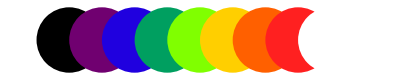

```mathematica
Graphics[Table[{Blend[{Black,Purple,Blue,Green,Yellow,Orange,Red,White},x],Disk[{8x,0}]},{x,0,1,1/8}]]
```

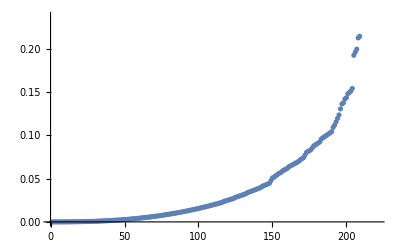

```mathematica
ListPlot@((Sort@DeleteDuplicates@Flatten@Rescale@Transpose@BinCounts[ReIm/@NestList[f,z0,iterates],{-1,1,1/res},{-1,1,1/res}])^(5/2))
```

```mathematica
Timing[dat=ReIm@NestList[f,z0,100000];
res=10;
epsilon=1*^-10;
indices=1+Floor[(1-epsilon) res Rescale[dat]];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->Total}];
matrix=SparseArray[indices->1.,{res,res}];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->First}];
Image[1-Rescale[matrix^(1/4)],ImageSize->Large]]
```

```mathematica
Timing[Image[Map[Blend[{Red,Orange,Yellow,Green,Blue, Purple, White,Black},#^4]&,1-Rescale[Normal[matrix]^(1/4)],{2}],ImageSize->Large]]
```

# Chaos

The behavior of f does seem chaotic.

```mathematica
f[f[f[z0]]]
f[f[f[z0+.01-.01I]]]
```

# Some plots of the function

```mathematica
Plot3D[Im[f[x+I y]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

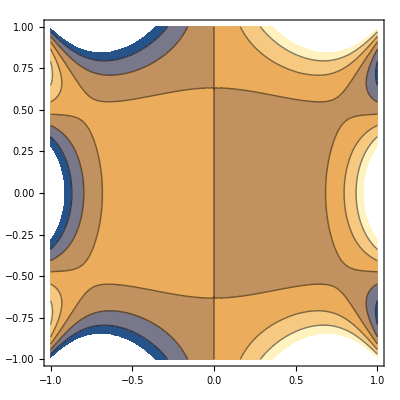

```mathematica
ContourPlot[Re[f[x+I y]],{x,-1,1},{y,-1,1}]
```

# Fractals

```mathematica
GraphicsGrid[Map[MandelbrotSetPlot[#1,ColorFunction->"SunsetColors",Frame->False]&,{{{0.2102 +0.464 I,0.4443 +0.7062 I},Apply[Complex,{{0.2274,0.5529},{0.2455,0.5717}},{1}]},{{},{-0.743+0.175 I,-0.723+0.195 I}}},{2}],ImageSize->600,Frame->All,FrameStyle->Gray]
```

-Graphics-

# Speed test: See https://mathematica.stackexchange.com/questions/211986/symmetric-icons

```mathematica
AbsoluteTiming[
dat=Quiet@ReIm@NestList[f,z0,10000000];
res=1000;
epsilon=1*^-10;
indices=1+Floor[(1-epsilon) res Rescale[dat]];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->Total}];
matrix=SparseArray[indices->1.,{res,res}];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->First}];]
```

{40.8578,Null}